# Perturbations in Warm Inflation (in the φ gauge) This code computes the background and perturbation evolutions in warm inflation (WI)

```mathematica
(* It is a good idea to start with a fresh kernel *)
Quit[]
```

```mathematica
(* Clean up leftover variables and start the kernel *)
ClearAll["Global`*"];
(* Move to the WI2easy directory through
SetDirectory["<path to WI2easy main directory (where WI2easy.m is located)>"];
or if using directly this main.nb notebook, then run: *)
SetDirectory[NotebookDirectory[]];

(* Load WI2easy *)
(*<<WI2easy.m*)
<<WI2easy_with-spectrumN.m
```

This is WI2easy v1.0

## Part 1: Definitions Parameters and model specific definitions (to be modified according to the model used) needed to run the code.

```mathematica
ParametersWI[]
```

```mathematica
(* Run the command below to check the values you have given *)

pars
```

<|Potential→(V0 x^4)/4,V0→1/100000000000000,PotentialType→quartic,HybridPotential→NO,InitialField→25,Dissipation→T,DissipationType→T,PotentialShape→0,Thermalized→1,RadNoise→1,gstar→100,Nefolds→60,ExtraParams→NO|>

```mathematica
(* OPTIONAL *)
(* The potential and dissipation function (along
with all parameters), can also be defined here.
These will overwrite any expressions given through
the ParametersWI[] command *)

(* the inflaton potential V0* function of x: x= inflaton in Mp units *)
potential=V0*x^4/4; 

(* initial value for V0   *)
V0init=10^(-14);

(* form of the dissipation coefficient: any function of T and x (do not include overall constant C_Upsilon) *)
funcdiss = T;

(* you can also define g_*, the radiation number of degrees of freedom here.
In this example we will use g_*=100. *)
gstar0 = 100;

(* Define next any extra parameters that the model might require. There are no extra parameters required in this example. *)
```

## Part 2: Running the background equations and finding appropriate initial conditions Evolution of the background equations for a given range of dissipation ratio Q=Υ/(3H). It produces the initial conditions corresponding to a scale about k=10.b3 H_0 before Hubble radius crossing (which corresponds to about 7 e-folds before Hubble radius crossing (k=aH). Use the command FindICs[Qi,Qf], giving the initial and final values of Q.

```mathematica
FindICs[10^(-9),4000]//AbsoluteTiming
```

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1.×10^-9

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=2.×10^-9

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=4.5×10^-9

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=7.×10^-9

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=9.5×10^-9

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1.2×10^-8

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=3.7×10^-8

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=6.2×10^-8

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=8.7×10^-8

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1.12×10^-7

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=3.62×10^-7

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=6.12×10^-7

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=8.62×10^-7

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1.112×10^-6

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=3.612×10^-6

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=6.112×10^-6

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=8.612×10^-6

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000011112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000021112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000031112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000041112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000051112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000061112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000071112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000081112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000091112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000101112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000201112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000301112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000401112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000501112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000601112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000701112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000801112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.000901112

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.00100111

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.00200111

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.00300111

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.00400111

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.00500111

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.00600111

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.00700111

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.00800111

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.00900111

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.0100011

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.0200011

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.0300011

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.0400011

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.0500011

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.0600011

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.0700011

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.0800011

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.0900011

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.100001

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.200001

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.300001

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.400001

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.500001

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.600001

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.700001

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.800001

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=0.900001

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=2.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=3.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=4.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=5.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=6.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=7.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=8.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=9.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=10.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=15.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=20.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=25.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=30.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=35.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=40.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=45.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=50.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=55.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=60.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=65.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=70.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=75.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=80.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=85.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=90.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=95.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=100.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=110.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=121.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=133.1

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=146.41

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=161.051

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=177.156

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=194.872

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=214.359

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=235.795

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=259.374

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=285.312

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=313.843

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=345.227

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=379.75

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=417.725

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=459.497

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=505.447

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=555.992

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=611.591

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=672.75

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=740.025

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=814.028

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=895.43

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=984.973

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1083.47

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1191.82

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1311.

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1442.1

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1586.31

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1744.94

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=1919.43

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=2111.38

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=2322.52

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=2554.77

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=2810.24

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=3091.27

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=3400.39

Finding the  ICs for Ntot= 60  efolds of inflation and for Q=3740.43

Finding the  ICs: Successful. Data files saved.

{1320.11,Null}

```mathematica
{354.029499,Null}
```

## Part 3: Running the perturbation (for the unnormalized spectrum) and generating data for G(Q) Evolution of the perturbation equations using the stochastic equations and obtaining the scalar power spectrum (in the φ = 0 gauge) from the Fokker-Planck equation. The data for the growth function G(Q) is obtained. Use the command FindGQ[] (with no arguments). It requires to run first FindICs[Qi,Qf] or to have the data file generated by FindICs.

```mathematica
(********** Perturbations Code ***********)
(*SetDirectory[NotebookDirectory[]]
SetOptions[OpenWrite,PageWidth->Infinity];*)
FindGQ[]//AbsoluteTiming
```

Finding now the value of G(Q) for Q=1.×10^-9

Q_*=1.13117×10^-9 , Spectrum=1.02132×10^-10 , Ps=1.01765×10^-10 , GQ*=1.0036

Finding now the value of G(Q) for Q=2.×10^-9

Q_*=2.26237×10^-9 , Spectrum=1.0213×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00358

Finding now the value of G(Q) for Q=4.5×10^-9

Q_*=5.09031×10^-9 , Spectrum=1.0213×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00358

Finding now the value of G(Q) for Q=7.×10^-9

Q_*=7.91824×10^-9 , Spectrum=1.0213×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00358

Finding now the value of G(Q) for Q=9.5×10^-9

Q_*=1.07462×10^-8 , Spectrum=1.0213×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00358

Finding now the value of G(Q) for Q=1.2×10^-8

Q_*=1.35741×10^-8 , Spectrum=1.0213×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00358

Finding now the value of G(Q) for Q=3.7×10^-8

Q_*=4.18536×10^-8 , Spectrum=1.0213×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00358

Finding now the value of G(Q) for Q=6.2×10^-8

Q_*=7.0133×10^-8 , Spectrum=1.0213×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00359

Finding now the value of G(Q) for Q=8.7×10^-8

Q_*=9.84125×10^-8 , Spectrum=1.02129×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00358

Finding now the value of G(Q) for Q=1.12×10^-7

Q_*=1.26692×10^-7 , Spectrum=1.0213×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00359

Finding now the value of G(Q) for Q=3.62×10^-7

Q_*=4.09486×10^-7 , Spectrum=1.02129×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00358

Finding now the value of G(Q) for Q=6.12×10^-7

Q_*=6.92281×10^-7 , Spectrum=1.02129×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00358

Finding now the value of G(Q) for Q=8.62×10^-7

Q_*=9.75076×10^-7 , Spectrum=1.02128×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00357

Finding now the value of G(Q) for Q=1.112×10^-6

Q_*=1.25787×10^-6 , Spectrum=1.02127×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00356

Finding now the value of G(Q) for Q=3.612×10^-6

Q_*=4.08582×10^-6 , Spectrum=1.02122×10^-10 , Ps=1.01765×10^-10 , GQ*=1.00351

Finding now the value of G(Q) for Q=6.112×10^-6

Q_*=6.91378×10^-6 , Spectrum=1.0212×10^-10 , Ps=1.01767×10^-10 , GQ*=1.00347

Finding now the value of G(Q) for Q=8.612×10^-6

Q_*=9.74174×10^-6 , Spectrum=1.02116×10^-10 , Ps=1.01769×10^-10 , GQ*=1.00342

Finding now the value of G(Q) for Q=0.000011112

Q_*=0.0000125697 , Spectrum=1.02111×10^-10 , Ps=1.01771×10^-10 , GQ*=1.00334

Finding now the value of G(Q) for Q=0.000021112

Q_*=0.0000238817 , Spectrum=1.02105×10^-10 , Ps=1.01784×10^-10 , GQ*=1.00316

Finding now the value of G(Q) for Q=0.000031112

Q_*=0.0000351937 , Spectrum=1.021×10^-10 , Ps=1.01801×10^-10 , GQ*=1.00294

Finding now the value of G(Q) for Q=0.000041112

Q_*=0.0000465059 , Spectrum=1.021×10^-10 , Ps=1.0182×10^-10 , GQ*=1.00275

Finding now the value of G(Q) for Q=0.000051112

Q_*=0.0000578182 , Spectrum=1.02098×10^-10 , Ps=1.01842×10^-10 , GQ*=1.00252

Finding now the value of G(Q) for Q=0.000061112

Q_*=0.0000691306 , Spectrum=1.02103×10^-10 , Ps=1.01865×10^-10 , GQ*=1.00233

Finding now the value of G(Q) for Q=0.000071112

Q_*=0.000080443 , Spectrum=1.0211×10^-10 , Ps=1.01891×10^-10 , GQ*=1.00215

Finding now the value of G(Q) for Q=0.000081112

Q_*=0.0000917557 , Spectrum=1.02116×10^-10 , Ps=1.01917×10^-10 , GQ*=1.00195

Finding now the value of G(Q) for Q=0.000091112

Q_*=0.000103068 , Spectrum=1.02125×10^-10 , Ps=1.01945×10^-10 , GQ*=1.00176

Finding now the value of G(Q) for Q=0.000101112

Q_*=0.000114381 , Spectrum=1.02136×10^-10 , Ps=1.01975×10^-10 , GQ*=1.00158

Finding now the value of G(Q) for Q=0.000201112

Q_*=0.000227515 , Spectrum=1.02297×10^-10 , Ps=1.02318×10^-10 , GQ*=0.999788

Finding now the value of G(Q) for Q=0.000301112

Q_*=0.00034066 , Spectrum=1.02537×10^-10 , Ps=1.0273×10^-10 , GQ*=0.998121

Finding now the value of G(Q) for Q=0.000401112

Q_*=0.000453816 , Spectrum=1.02834×10^-10 , Ps=1.03191×10^-10 , GQ*=0.996542

Finding now the value of G(Q) for Q=0.000501112

Q_*=0.000566983 , Spectrum=1.03178×10^-10 , Ps=1.0369×10^-10 , GQ*=0.995056

Finding now the value of G(Q) for Q=0.000601112

Q_*=0.000680161 , Spectrum=1.03558×10^-10 , Ps=1.04222×10^-10 , GQ*=0.993626

Finding now the value of G(Q) for Q=0.000701112

Q_*=0.000793349 , Spectrum=1.03972×10^-10 , Ps=1.04781×10^-10 , GQ*=0.992272

Finding now the value of G(Q) for Q=0.000801112

Q_*=0.000906549 , Spectrum=1.04415×10^-10 , Ps=1.05365×10^-10 , GQ*=0.99098

Finding now the value of G(Q) for Q=0.000901112

Q_*=0.00101976 , Spectrum=1.04883×10^-10 , Ps=1.05971×10^-10 , GQ*=0.989734

Finding now the value of G(Q) for Q=0.00100111

Q_*=0.00113298 , Spectrum=1.05376×10^-10 , Ps=1.06597×10^-10 , GQ*=0.988545

Finding now the value of G(Q) for Q=0.00200111

Q_*=0.0022658 , Spectrum=1.11285×10^-10 , Ps=1.13662×10^-10 , GQ*=0.97909

Finding now the value of G(Q) for Q=0.00300111

Q_*=0.00339971 , Spectrum=1.18421×10^-10 , Ps=1.21712×10^-10 , GQ*=0.972959

Finding now the value of G(Q) for Q=0.00400111

Q_*=0.00453472 , Spectrum=1.26365×10^-10 , Ps=1.30387×10^-10 , GQ*=0.969158

Finding now the value of G(Q) for Q=0.00500111

Q_*=0.00567084 , Spectrum=1.34891×10^-10 , Ps=1.39493×10^-10 , GQ*=0.967007

Finding now the value of G(Q) for Q=0.00600111

Q_*=0.00680803 , Spectrum=1.43854×10^-10 , Ps=1.48911×10^-10 , GQ*=0.966037

Finding now the value of G(Q) for Q=0.00700111

Q_*=0.00794631 , Spectrum=1.53154×10^-10 , Ps=1.58559×10^-10 , GQ*=0.965913

Finding now the value of G(Q) for Q=0.00800111

Q_*=0.00908564 , Spectrum=1.62708×10^-10 , Ps=1.68376×10^-10 , GQ*=0.966338

Finding now the value of G(Q) for Q=0.00900111

Q_*=0.010226 , Spectrum=1.72485×10^-10 , Ps=1.78317×10^-10 , GQ*=0.967295

Finding now the value of G(Q) for Q=0.0100011

Q_*=0.0113674 , Spectrum=1.82418×10^-10 , Ps=1.88348×10^-10 , GQ*=0.968516

Finding now the value of G(Q) for Q=0.0200011

Q_*=0.0228316 , Spectrum=2.85176×10^-10 , Ps=2.89491×10^-10 , GQ*=0.985097

Finding now the value of G(Q) for Q=0.0300011

Q_*=0.0343733 , Spectrum=3.85965×10^-10 , Ps=3.86431×10^-10 , GQ*=0.998794

Finding now the value of G(Q) for Q=0.0400011

Q_*=0.0459781 , Spectrum=4.80331×10^-10 , Ps=4.76402×10^-10 , GQ*=1.00825

Finding now the value of G(Q) for Q=0.0500011

Q_*=0.0576361 , Spectrum=5.67259×10^-10 , Ps=5.59032×10^-10 , GQ*=1.01472

Finding now the value of G(Q) for Q=0.0600011

Q_*=0.06934 , Spectrum=6.4685×10^-10 , Ps=6.34668×10^-10 , GQ*=1.0192

Finding now the value of G(Q) for Q=0.0700011

Q_*=0.081084 , Spectrum=7.19621×10^-10 , Ps=7.03872×10^-10 , GQ*=1.02237

Finding now the value of G(Q) for Q=0.0800011

Q_*=0.0928633 , Spectrum=7.86234×10^-10 , Ps=7.67255×10^-10 , GQ*=1.02474

Finding now the value of G(Q) for Q=0.0900011

Q_*=0.104674 , Spectrum=8.47322×10^-10 , Ps=8.25399×10^-10 , GQ*=1.02656

Finding now the value of G(Q) for Q=0.100001

Q_*=0.116513 , Spectrum=9.03523×10^-10 , Ps=8.78843×10^-10 , GQ*=1.02808

Finding now the value of G(Q) for Q=0.200001

Q_*=0.235957 , Spectrum=1.2934×10^-9 , Ps=1.23817×10^-9 , GQ*=1.0446

Finding now the value of G(Q) for Q=0.300001

Q_*=0.356441 , Spectrum=1.5341×10^-9 , Ps=1.4262×10^-9 , GQ*=1.07566

Finding now the value of G(Q) for Q=0.400001

Q_*=0.477354 , Spectrum=1.72173×10^-9 , Ps=1.53841×10^-9 , GQ*=1.11917

Finding now the value of G(Q) for Q=0.500001

Q_*=0.598439 , Spectrum=1.88769×10^-9 , Ps=1.6116×10^-9 , GQ*=1.17132

Finding now the value of G(Q) for Q=0.600001

Q_*=0.719576 , Spectrum=2.04441×10^-9 , Ps=1.66246×10^-9 , GQ*=1.22975

Finding now the value of G(Q) for Q=0.700001

Q_*=0.840711 , Spectrum=2.19759×10^-9 , Ps=1.69953×10^-9 , GQ*=1.29306

Finding now the value of G(Q) for Q=0.800001

Q_*=0.961816 , Spectrum=2.35014×10^-9 , Ps=1.72756×10^-9 , GQ*=1.36038

Finding now the value of G(Q) for Q=0.900001

Q_*=1.08288 , Spectrum=2.50369×10^-9 , Ps=1.74939×10^-9 , GQ*=1.43117

Finding now the value of G(Q) for Q=1.

Q_*=1.2039 , Spectrum=2.65917×10^-9 , Ps=1.76681×10^-9 , GQ*=1.50507

Finding now the value of G(Q) for Q=2.

Q_*=2.41202 , Spectrum=4.38749×10^-9 , Ps=1.8428×10^-9 , GQ*=2.38088

Finding now the value of G(Q) for Q=3.

Q_*=3.61795 , Spectrum=6.4758×10^-9 , Ps=1.86625×10^-9 , GQ*=3.46996

Finding now the value of G(Q) for Q=4.

Q_*=4.8229 , Spectrum=8.93225×10^-9 , Ps=1.87736×10^-9 , GQ*=4.75788

Finding now the value of G(Q) for Q=5.

Q_*=6.02736 , Spectrum=1.17596×10^-8 , Ps=1.88379×10^-9 , GQ*=6.24254

Finding now the value of G(Q) for Q=6.

Q_*=7.23153 , Spectrum=1.49631×10^-8 , Ps=1.88796×10^-9 , GQ*=7.92556

Finding now the value of G(Q) for Q=7.

Q_*=8.43552 , Spectrum=1.85501×10^-8 , Ps=1.89088×10^-9 , GQ*=9.8103

Finding now the value of G(Q) for Q=8.

Q_*=9.63939 , Spectrum=2.2529×10^-8 , Ps=1.89304×10^-9 , GQ*=11.901

Finding now the value of G(Q) for Q=9.

Q_*=10.8432 , Spectrum=2.69092×10^-8 , Ps=1.89469×10^-9 , GQ*=14.2024

Finding now the value of G(Q) for Q=10.

Q_*=12.0469 , Spectrum=3.17003×10^-8 , Ps=1.89601×10^-9 , GQ*=16.7195

Finding now the value of G(Q) for Q=15.

Q_*=18.065 , Spectrum=6.21805×10^-8 , Ps=1.89987×10^-9 , GQ*=32.7289

Finding now the value of G(Q) for Q=20.

Q_*=24.0827 , Spectrum=1.04493×10^-7 , Ps=1.90175×10^-9 , GQ*=54.9457

Finding now the value of G(Q) for Q=25.

Q_*=30.1003 , Spectrum=1.59946×10^-7 , Ps=1.90287×10^-9 , GQ*=84.0552

Finding now the value of G(Q) for Q=30.

Q_*=36.1177 , Spectrum=2.29832×10^-7 , Ps=1.90361×10^-9 , GQ*=120.735

Finding now the value of G(Q) for Q=35.

Q_*=42.1351 , Spectrum=3.15427×10^-7 , Ps=1.90413×10^-9 , GQ*=165.654

Finding now the value of G(Q) for Q=40.

Q_*=48.1525 , Spectrum=4.1799×10^-7 , Ps=1.90452×10^-9 , GQ*=219.472

Finding now the value of G(Q) for Q=45.

Q_*=54.1698 , Spectrum=5.38763×10^-7 , Ps=1.90483×10^-9 , GQ*=282.841

Finding now the value of G(Q) for Q=50.

Q_*=60.1871 , Spectrum=6.78981×10^-7 , Ps=1.90506×10^-9 , GQ*=356.41

Finding now the value of G(Q) for Q=55.

Q_*=66.2044 , Spectrum=8.39862×10^-7 , Ps=1.90527×10^-9 , GQ*=440.811

Finding now the value of G(Q) for Q=60.

Q_*=72.2217 , Spectrum=1.02262×10^-6 , Ps=1.90543×10^-9 , GQ*=536.686

Finding now the value of G(Q) for Q=65.

Q_*=78.239 , Spectrum=1.22844×10^-6 , Ps=1.90557×10^-9 , GQ*=644.66

Finding now the value of G(Q) for Q=70.

Q_*=84.2563 , Spectrum=1.45855×10^-6 , Ps=1.90569×10^-9 , GQ*=765.365

Finding now the value of G(Q) for Q=75.

Q_*=90.2736 , Spectrum=1.7141×10^-6 , Ps=1.90579×10^-9 , GQ*=899.419

Finding now the value of G(Q) for Q=80.

Q_*=96.2909 , Spectrum=1.9963×10^-6 , Ps=1.90588×10^-9 , GQ*=1047.44

Finding now the value of G(Q) for Q=85.

Q_*=102.308 , Spectrum=2.3063×10^-6 , Ps=1.90596×10^-9 , GQ*=1210.05

Finding now the value of G(Q) for Q=90.

Q_*=108.325 , Spectrum=2.64529×10^-6 , Ps=1.90603×10^-9 , GQ*=1387.85

Finding now the value of G(Q) for Q=95.

Q_*=114.343 , Spectrum=3.01442×10^-6 , Ps=1.90609×10^-9 , GQ*=1581.47

Finding now the value of G(Q) for Q=100.

Q_*=120.36 , Spectrum=3.41486×10^-6 , Ps=1.90615×10^-9 , GQ*=1791.5

Finding now the value of G(Q) for Q=110.

Q_*=132.395 , Spectrum=4.31428×10^-6 , Ps=1.90625×10^-9 , GQ*=2263.23

Finding now the value of G(Q) for Q=121.

Q_*=145.633 , Spectrum=5.46457×10^-6 , Ps=1.90634×10^-9 , GQ*=2866.53

Finding now the value of G(Q) for Q=133.1

Q_*=160.194 , Spectrum=6.93884×10^-6 , Ps=1.90642×10^-9 , GQ*=3639.73

Finding now the value of G(Q) for Q=146.41

Q_*=176.212 , Spectrum=8.83198×10^-6 , Ps=1.90649×10^-9 , GQ*=4632.58

Finding now the value of G(Q) for Q=161.051

Q_*=193.832 , Spectrum=0.0000112676 , Ps=1.90655×10^-9 , GQ*=5909.95

Finding now the value of G(Q) for Q=177.156

Q_*=213.214 , Spectrum=0.0000144067 , Ps=1.90662×10^-9 , GQ*=7556.18

Finding now the value of G(Q) for Q=194.872

Q_*=234.534 , Spectrum=0.0000184596 , Ps=1.90667×10^-9 , GQ*=9681.61

Finding now the value of G(Q) for Q=214.359

Q_*=257.986 , Spectrum=0.0000237018 , Ps=1.90672×10^-9 , GQ*=12430.7

Finding now the value of G(Q) for Q=235.795

Q_*=283.783 , Spectrum=0.0000304922 , Ps=1.90677×10^-9 , GQ*=15991.6

Finding now the value of G(Q) for Q=259.374

Q_*=312.159 , Spectrum=0.0000393031 , Ps=1.90681×10^-9 , GQ*=20612.

Finding now the value of G(Q) for Q=285.312

Q_*=343.374 , Spectrum=0.0000507473 , Ps=1.90683×10^-9 , GQ*=26613.4

Finding now the value of G(Q) for Q=313.843

Q_*=377.71 , Spectrum=0.0000656409 , Ps=1.9069×10^-9 , GQ*=34422.9

Finding now the value of G(Q) for Q=345.227

Q_*=415.479 , Spectrum=0.0000850438 , Ps=1.90691×10^-9 , GQ*=44597.6

Finding now the value of G(Q) for Q=379.75

Q_*=457.026 , Spectrum=0.000110353 , Ps=1.90693×10^-9 , GQ*=57869.3

Finding now the value of G(Q) for Q=417.725

Q_*=502.727 , Spectrum=0.000143409 , Ps=1.90696×10^-9 , GQ*=75202.8

Finding now the value of G(Q) for Q=459.497

Q_*=552.998 , Spectrum=0.000186633 , Ps=1.90696×10^-9 , GQ*=97869.6

Finding now the value of G(Q) for Q=505.447

Q_*=608.296 , Spectrum=0.000243211 , Ps=1.90699×10^-9 , GQ*=127537.

Finding now the value of G(Q) for Q=555.992

Q_*=669.124 , Spectrum=0.000317344 , Ps=1.90702×10^-9 , GQ*=166409.

Finding now the value of G(Q) for Q=611.591

Q_*=736.035 , Spectrum=0.000414577 , Ps=1.90708×10^-9 , GQ*=217389.

Finding now the value of G(Q) for Q=672.75

Q_*=809.637 , Spectrum=0.000542241 , Ps=1.90707×10^-9 , GQ*=284332.

Finding now the value of G(Q) for Q=740.025

Q_*=890.6 , Spectrum=0.000709953 , Ps=1.90716×10^-9 , GQ*=372257.

Finding now the value of G(Q) for Q=814.028

Q_*=979.658 , Spectrum=0.000930681 , Ps=1.90706×10^-9 , GQ*=488018.

Finding now the value of G(Q) for Q=895.43

Q_*=1077.62 , Spectrum=0.00122081 , Ps=1.90706×10^-9 , GQ*=640154.

Finding now the value of G(Q) for Q=984.973

Q_*=1185.38 , Spectrum=0.00160338 , Ps=1.90713×10^-9 , GQ*=840733.

Finding now the value of G(Q) for Q=1083.47

Q_*=1303.92 , Spectrum=0.00210684 , Ps=1.90716×10^-9 , GQ*=1.1047×10^6

Finding now the value of G(Q) for Q=1191.82

Q_*=1434.31 , Spectrum=0.00277155 , Ps=1.90712×10^-9 , GQ*=1.45326×10^6

Finding now the value of G(Q) for Q=1311.

Q_*=1577.74 , Spectrum=0.00364913 , Ps=1.90711×10^-9 , GQ*=1.91343×10^6

Finding now the value of G(Q) for Q=1442.1

Q_*=1735.51 , Spectrum=0.00480677 , Ps=1.90715×10^-9 , GQ*=2.52039×10^6

Finding now the value of G(Q) for Q=1586.31

Q_*=1909.06 , Spectrum=0.00633461 , Ps=1.90729×10^-9 , GQ*=3.32126×10^6

Finding now the value of G(Q) for Q=1744.94

Q_*=2099.97 , Spectrum=0.00835821 , Ps=1.90716×10^-9 , GQ*=4.38254×10^6

Finding now the value of G(Q) for Q=1919.43

Q_*=2309.96 , Spectrum=0.0110347 , Ps=1.90737×10^-9 , GQ*=5.78531×10^6

Finding now the value of G(Q) for Q=2111.38

Q_*=2540.96 , Spectrum=0.0145738 , Ps=1.90714×10^-9 , GQ*=7.64173×10^6

Finding now the value of G(Q) for Q=2322.52

Q_*=2795.05 , Spectrum=0.0192506 , Ps=1.90722×10^-9 , GQ*=1.00936×10^7

Finding now the value of G(Q) for Q=2554.77

Q_*=3074.55 , Spectrum=0.0254652 , Ps=1.90698×10^-9 , GQ*=1.33537×10^7

Finding now the value of G(Q) for Q=2810.24

Q_*=3382.01 , Spectrum=0.033636 , Ps=1.90722×10^-9 , GQ*=1.76362×10^7

Finding now the value of G(Q) for Q=3091.27

Q_*=3720.21 , Spectrum=0.0445107 , Ps=1.90771×10^-9 , GQ*=2.3332×10^7

Finding now the value of G(Q) for Q=3400.39

Q_*=4092.23 , Spectrum=0.0589163 , Ps=1.90699×10^-9 , GQ*=3.08949×10^7

Finding now the value of G(Q) for Q=3740.43

Q_*=4501.45 , Spectrum=0.0780025 , Ps=1.90723×10^-9 , GQ*=4.08983×10^7

Finding G(Q): Successful. Data file saved.

{2472.88,Null}

## Part 4: Normalizing the spectrum and obtaining the observable quantities (for a single value of Q) Using the data for the growth function G(Q), the data is interpolated and the full scalar of curvature power spectrum is used to: normalize the spectrum with the COBE normalization and the observables (the tensor-to-scalar ratio r, spectral tilt n_s and running α_s) are obtained for a given value of Q. Use the command ObservationsWI[Q,phi] given the values of Q and phi (in units of reduced Planck mass). It requires to run first FindICs[Qi,Qf] and FindGQ[], or to have the data files generated by them.

```mathematica
ObservationsWI[1,7]//AbsoluteTiming
```

Running now spectrum code for Q=1..Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00003 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0250809 , V_0=3.19972×10^-15 , Q_*=1.02525 , r(N_*)=0.000337437 , ns(N_*)=0.968803 , alphas(N_*)=-0.000285172

{34.2288,{0.0250809,3.19972×10^-15,1.02525,0.000337437,0.968803,-0.000285172}}

```mathematica
(* You can check the values of some key results here *)

Print["Q_*=",Qdiss[Nstar]," , ","epsilon(Nfinal)=",epsilon0[Nend]," , ","spectrum(N_*)=",spectrum[Nstar]," , ","r(N_*)=",rtensor[Nstar]," , ","ns(N_*)=",ns[Nstar]," , ","phi(N_*)/Mp= ",phi[Nstar]," , ","Δϕ/Mp= ",phi[Nstar]-phi[Nend]," , ","temp_end(GeV)= ",Mpl*(V0xstar*rad[Nend]/Cr0)^(1/4)," , ","N*= ",Nend-Nstar," , ","Ntot= ",Ntot," , ","C_Upsilon= ",CUpsilon," , ","V0(GeV^4)= ",V0xstar*Mpl^4," , ","V0/Mp^4= ",V0xstar," , ","V*(GeV^4)= ",Mpl^4*(pot/.{x->phi[Nstar],V0->V0xstar})^(1/4)," , ","epsilonV*= ",(epsilonsr/.x->phi[Nstar])," , ","etaV*= ",(etasr/.x->phi[Nstar])," , ","V*^{1/4}/Mpl= ",((pot/.{x->phi[Nstar],V0->V0xstar}))^(1/4)," , ","T/H(N_*)= ",TH[Nstar]];
```

Q_*=1.02525 , epsilon(Nfinal)=1.00003 , spectrum(N_*)=2.10521×10^-9 , r(N_*)=0.000337437 , ns(N_*)=0.968803 , phi(N_*)/Mp= 10.6695 , Δϕ/Mp= 10.5307 , temp_end(GeV)= 5.64005×10^9 , N*= 58.137 , Ntot= 59.0794 , C_Upsilon= 0.0250809 , V0(GeV^4)= 1.12625×10^59 , V0/Mp^4= 3.19972×10^-15 , V*(GeV^4)= 6.31584×10^70 , epsilonV*= 0.0702754 , etaV*= 0.105413 , V*^{1/4}/Mpl= 0.00179435 , T/H(N_*)= 122.633

Making background plots for Q_*=1.

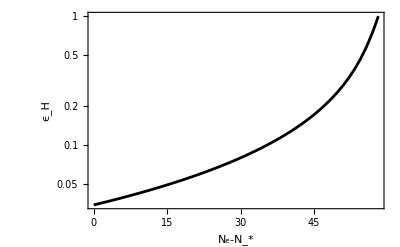

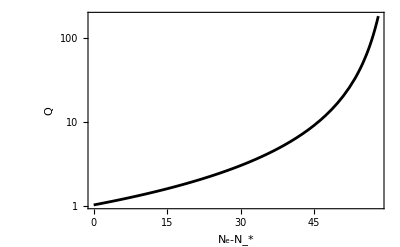

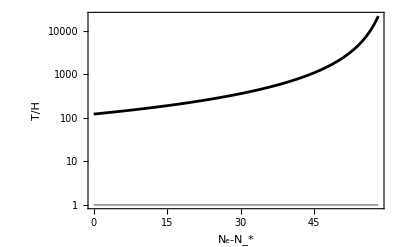

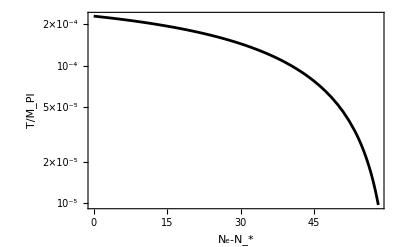

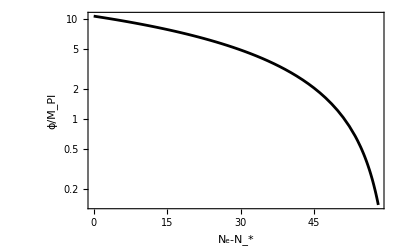

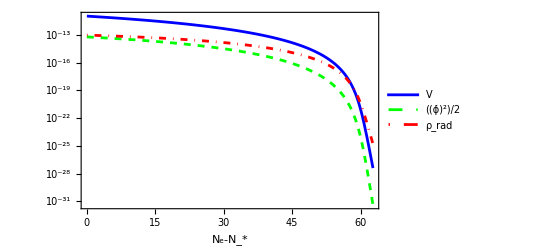

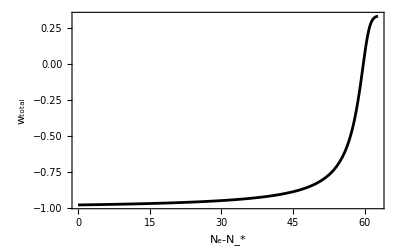

Spectrum as a function of the number of efolds, k_*/k_pivot,
and k_*. Results are cut at maximum Q in the G(Q) data to avoid going beyond a region where data
are not available.

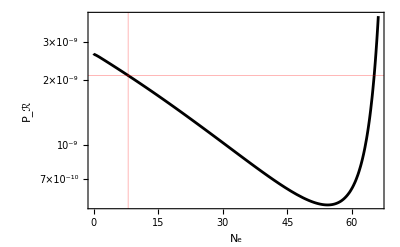

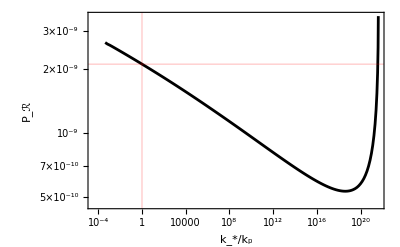

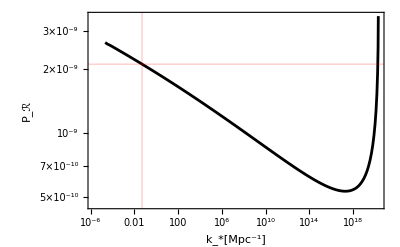

```mathematica
(* Plotting background quantities: slow-row coefficient Subscript[ϵ, H], Dissipation ratio Q, T/H, T, ϕ, equation of state, energy densities, all as a function of the number of efolds. The complete form of the spectrum is also generated *)

MakePlotsEvolution
```

## Part 5: Find the spectrum P_R as a function of the scale k (for a single value of Q) Using the expressions for the perturbations and the normalized spectrum, the spectrum as a function of the number of e-folds is found (for a fixed value of Q). Use the command WIspectrum[Q,phi] given the values of Q and phi (in units of reduced Planck mass). The spectrum evolution is available through the function Spectrumk[ne].

```mathematica
WIspectrumk[1,7]
```

Running now the normalized spectrum code for 
Q=1.

Running now spectrum code for Q=1..Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00012 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.025081 , V_0=3.20165×10^-15 , Q_*=1.02526 , r(N_*)=0.000337502 , ns(N_*)=0.968797 , alphas(N_*)=-0.00028529

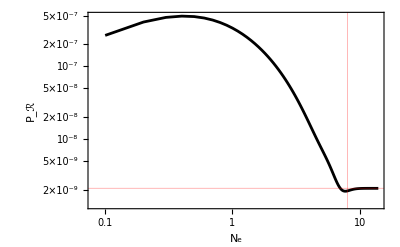

```mathematica
ListLogLogPlot[Table[{t,Spectrumk[t]},{t,0.1,Npert,0.1}],PlotStyle->{Black},Frame->True,Joined->True,FrameLabel->{Style["N_e",14,Italic,Black],Style["P_ℛ",Italic,14,Black]},FrameTicksStyle->Directive[Black,12],PlotRange->All,GridLines->{{{Nstar,Red}},{{Pcurv,Red}}}]
```

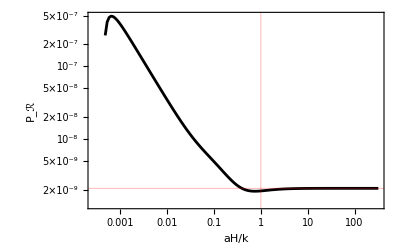

```mathematica
ListLogLogPlot[Table[{(Exp[t] Hubble[t])/kstar,Spectrumk[t]},{t,0.1,Npert,0.1}],PlotStyle->{Black},Frame->True,Joined->True,FrameLabel->{Style["aH/k",14,Italic,Black],Style["P_ℛ",Italic,14,Black]},FrameTicksStyle->Directive[Black,12],PlotRange->All,GridLines->{{{1,Red}},{{Pcurv,Red}}}]
```

```mathematica
spectrum[Nstar]
```

2.10521×10^-9

```mathematica
Spectrumk[Npert]
```

2.09954×10^-9

```mathematica
plot=ListLogLogPlot[Table[{(Exp[t] Hubble[t])/kstar*kpivotscale,spectrum[t]},{t,0.1,Npert,0.1}],PlotStyle->{Black},Frame->True,Joined->True,FrameLabel->{Style["k_*[Mpc^-1]",14,Italic,Black],Style["P_ℛ",Italic,14,Black]},FrameTicksStyle->Directive[Black,12],PlotRange->All,GridLines->{{{kpivotscale,Red}},{{Pcurv,Red}}}];
```

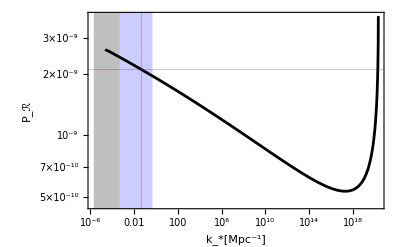

```mathematica
(*Extract the y-axis range*)
yrange=PlotRange[plot][[2]]; 

ListLogLogPlot[Table[{(Exp[t] Hubble[t])/kstar*kpivotscale,spectrum[t]},{t,0.1,Nend,0.1}],PlotStyle->{Black},Frame->True,Joined->True,FrameLabel->{Style["k_*[Mpc^-1]",14,Italic,Black],Style["P_ℛ",Italic,14,Black]},FrameTicksStyle->Directive[Black,12],GridLines->{{{kpivotscale,Red}},{{Pcurv,Red}}},PlotRange->All,Prolog->{Gray,Opacity[0.5],Rectangle[{Log[0.1*(Exp[0] Hubble[0])/kstar*kpivotscale],yrange[[1]]*10},{Log[0.0005],yrange[[2]]*0.1}],Blue,Opacity[0.2],Rectangle[{Log[0.0005],yrange[[1]]*10},{Log[0.5],yrange[[2]]*0.1}]}]
```

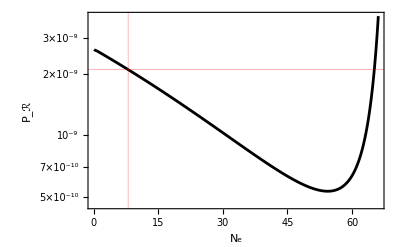

```mathematica
ListLogPlot[Table[{t,spectrum[t]},{t,0.1,Nend,0.1}],PlotStyle->{Black},Frame->True,Joined->True,FrameLabel->{Style["N_e",14,Italic,Black],Style["P_ℛ",Italic,14,Black]},FrameTicksStyle->Directive[Black,12],PlotRange->All,GridLines->{{{Nstar,Red}},{{Pcurv,Red}}}]
```

## Part 6: Find the observables (at N_*for different values of Q_*) Obtain several background and perturbation quantities when the value of Q at Hubble crossing is varied. Use the command QrangeWI[Qinit] (with loop starting at the value Qinit). It requires to run first FindICs[Qi,Qf] and FindGQ[], or to have the data files generated by them. It generates background quantities (phi, \dot \phi, T/H, T/Mp, H, V0, Cupsilon, etc) and the observables (n_s, r, \alpha_s) all as a function of Q at Hubble crossing.

```mathematica
(* Evolving the perturbations starting for N_* for different values of scale k *)

(*SetDirectory[NotebookDirectory[]]
SetOptions[OpenWrite,PageWidth->Infinity];*)
```

```mathematica
QrangeWI[10^(-9)]//AbsoluteTiming
```

Finding observables as a function of Q_*

Running now spectrum code for Q=2.×10^-9.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00005 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=3.92742×10^-8 , V_0=1.28559×10^-13 , Q_*=2.00714×10^-9 , r(N_*)=0.255534 , ns(N_*)=0.951175 , alphas(N_*)=-0.000805414

Running now spectrum code for Q=4.5×10^-9.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00013 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=7.21521×10^-8 , V_0=1.30042×10^-13 , Q_*=4.51613×10^-9 , r(N_*)=0.256512 , ns(N_*)=0.950986 , alphas(N_*)=-0.000811718

Running now spectrum code for Q=7.×10^-9.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00027 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=1.005×10^-7 , V_0=1.30678×10^-13 , Q_*=7.02512×10^-9 , r(N_*)=0.256928 , ns(N_*)=0.950905 , alphas(N_*)=-0.000814414

Running now spectrum code for Q=9.5×10^-9.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00036 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=1.26368×10^-7 , V_0=1.3122×10^-13 , Q_*=9.53414×10^-9 , r(N_*)=0.257283 , ns(N_*)=0.950837 , alphas(N_*)=-0.000816713

Running now spectrum code for Q=1.2×10^-8.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.0004 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=1.50567×10^-7 , V_0=1.31345×10^-13 , Q_*=1.20431×10^-8 , r(N_*)=0.257364 , ns(N_*)=0.950821 , alphas(N_*)=-0.000817241

Running now spectrum code for Q=3.7×10^-8.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00028 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=3.50349×10^-7 , V_0=1.33201×10^-13 , Q_*=3.71337×10^-8 , r(N_*)=0.258569 , ns(N_*)=0.950587 , alphas(N_*)=-0.000825071

Running now spectrum code for Q=6.2×10^-8.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00027 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=5.15993×10^-7 , V_0=1.33876×10^-13 , Q_*=6.22243×10^-8 , r(N_*)=0.259002 , ns(N_*)=0.950503 , alphas(N_*)=-0.000827954

Running now spectrum code for Q=8.7×10^-8.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00029 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=6.65261×10^-7 , V_0=1.34652×10^-13 , Q_*=8.73154×10^-8 , r(N_*)=0.259502 , ns(N_*)=0.950405 , alphas(N_*)=-0.00083114

Running now spectrum code for Q=1.12×10^-7.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00005 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=8.04021×10^-7 , V_0=1.34851×10^-13 , Q_*=1.12406×10^-7 , r(N_*)=0.25963 , ns(N_*)=0.950382 , alphas(N_*)=-0.000831889

Running now spectrum code for Q=3.62×10^-7.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00034 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=1.93816×10^-6 , V_0=1.36914×10^-13 , Q_*=3.6332×10^-7 , r(N_*)=0.260944 , ns(N_*)=0.950125 , alphas(N_*)=-0.000840663

Running now spectrum code for Q=6.12×10^-7.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00031 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=2.8736×10^-6 , V_0=1.37809×10^-13 , Q_*=6.14236×10^-7 , r(N_*)=0.261511 , ns(N_*)=0.950016 , alphas(N_*)=-0.000844404

Running now spectrum code for Q=8.62×10^-7.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00004 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=3.71531×10^-6 , V_0=1.38403×10^-13 , Q_*=8.65154×10^-7 , r(N_*)=0.261886 , ns(N_*)=0.949943 , alphas(N_*)=-0.000846867

Running now spectrum code for Q=1.112×10^-6.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00018 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=4.49723×10^-6 , V_0=1.38777×10^-13 , Q_*=1.11607×10^-6 , r(N_*)=0.262122 , ns(N_*)=0.949898 , alphas(N_*)=-0.000848414

Running now spectrum code for Q=3.612×10^-6.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00019 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0000108814 , V_0=1.40981×10^-13 , Q_*=3.6253×10^-6 , r(N_*)=0.263505 , ns(N_*)=0.94963 , alphas(N_*)=-0.000857526

Running now spectrum code for Q=6.112×10^-6.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00041 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0000161442 , V_0=1.41946×10^-13 , Q_*=6.13455×10^-6 , r(N_*)=0.264105 , ns(N_*)=0.949515 , alphas(N_*)=-0.000861531

Running now spectrum code for Q=8.612×10^-6.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00039 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0000208791 , V_0=1.42363×10^-13 , Q_*=8.6438×10^-6 , r(N_*)=0.264365 , ns(N_*)=0.949464 , alphas(N_*)=-0.000863275

Running now spectrum code for Q=0.000011112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00008 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0000252774 , V_0=1.42793×10^-13 , Q_*=0.0000111531 , r(N_*)=0.264636 , ns(N_*)=0.949412 , alphas(N_*)=-0.00086509

Running now spectrum code for Q=0.000021112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00034 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0000409069 , V_0=1.44158×10^-13 , Q_*=0.0000211903 , r(N_*)=0.265483 , ns(N_*)=0.949255 , alphas(N_*)=-0.000870456

Running now spectrum code for Q=0.000031112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00008 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0000547146 , V_0=1.44884×10^-13 , Q_*=0.0000312276 , r(N_*)=0.265934 , ns(N_*)=0.949169 , alphas(N_*)=-0.000873089

Running now spectrum code for Q=0.000041112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00011 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0000674356 , V_0=1.45434×10^-13 , Q_*=0.0000412649 , r(N_*)=0.266272 , ns(N_*)=0.94911 , alphas(N_*)=-0.000875494

Running now spectrum code for Q=0.000051112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00032 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0000793979 , V_0=1.45606×10^-13 , Q_*=0.0000513022 , r(N_*)=0.26638 , ns(N_*)=0.949088 , alphas(N_*)=-0.000876323

Running now spectrum code for Q=0.000061112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00031 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0000907858 , V_0=1.46283×10^-13 , Q_*=0.0000613397 , r(N_*)=0.266794 , ns(N_*)=0.949016 , alphas(N_*)=-0.000877638

Running now spectrum code for Q=0.000071112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00024 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000101714 , V_0=1.46317×10^-13 , Q_*=0.000071377 , r(N_*)=0.266811 , ns(N_*)=0.949016 , alphas(N_*)=-0.000878284

Running now spectrum code for Q=0.000081112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.0003 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000112263 , V_0=1.46749×10^-13 , Q_*=0.0000814146 , r(N_*)=0.267068 , ns(N_*)=0.948966 , alphas(N_*)=-0.000880081

Running now spectrum code for Q=0.000091112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00002 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000122491 , V_0=1.46745×10^-13 , Q_*=0.0000914519 , r(N_*)=0.267063 , ns(N_*)=0.94897 , alphas(N_*)=-0.000879274

Running now spectrum code for Q=0.000101112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00008 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000132442 , V_0=1.47049×10^-13 , Q_*=0.00010149 , r(N_*)=0.267241 , ns(N_*)=0.94894 , alphas(N_*)=-0.00088018

Running now spectrum code for Q=0.000201112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00039 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000221801 , V_0=1.4849×10^-13 , Q_*=0.000201866 , r(N_*)=0.268004 , ns(N_*)=0.948811 , alphas(N_*)=-0.000883577

Running now spectrum code for Q=0.000301112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00035 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00030016 , V_0=1.49278×10^-13 , Q_*=0.000302244 , r(N_*)=0.268306 , ns(N_*)=0.948768 , alphas(N_*)=-0.000883745

Running now spectrum code for Q=0.000401112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00023 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000372091 , V_0=1.50295×10^-13 , Q_*=0.000402624 , r(N_*)=0.268693 , ns(N_*)=0.9487 , alphas(N_*)=-0.000884393

Running now spectrum code for Q=0.000501112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00028 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00043956 , V_0=1.50593×10^-13 , Q_*=0.000503005 , r(N_*)=0.268611 , ns(N_*)=0.948721 , alphas(N_*)=-0.000881908

Running now spectrum code for Q=0.000601112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00039 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000503651 , V_0=1.50753×10^-13 , Q_*=0.000603387 , r(N_*)=0.268414 , ns(N_*)=0.948756 , alphas(N_*)=-0.000879357

Running now spectrum code for Q=0.000701112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00016 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000565046 , V_0=1.50976×10^-13 , Q_*=0.00070377 , r(N_*)=0.268225 , ns(N_*)=0.94879 , alphas(N_*)=-0.000875943

Running now spectrum code for Q=0.000801112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00014 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000624205 , V_0=1.51391×10^-13 , Q_*=0.000804157 , r(N_*)=0.268123 , ns(N_*)=0.948803 , alphas(N_*)=-0.000873834

Running now spectrum code for Q=0.000901112.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00025 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000681459 , V_0=1.51374×10^-13 , Q_*=0.000904543 , r(N_*)=0.267742 , ns(N_*)=0.948865 , alphas(N_*)=-0.000870102

Running now spectrum code for Q=0.00100111.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00014 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.000737062 , V_0=1.51561×10^-13 , Q_*=0.00100493 , r(N_*)=0.26746 , ns(N_*)=0.948906 , alphas(N_*)=-0.000866344

Running now spectrum code for Q=0.00200111.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00018 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00123138 , V_0=1.51495×10^-13 , Q_*=0.00200892 , r(N_*)=0.262623 , ns(N_*)=0.949595 , alphas(N_*)=-0.000823061

Running now spectrum code for Q=0.00300111.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00015 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0016557 , V_0=1.50779×10^-13 , Q_*=0.00301312 , r(N_*)=0.256365 , ns(N_*)=0.950407 , alphas(N_*)=-0.000776056

Running now spectrum code for Q=0.00400111.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00026 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00203589 , V_0=1.47752×10^-13 , Q_*=0.00401751 , r(N_*)=0.248232 , ns(N_*)=0.951482 , alphas(N_*)=-0.000723071

Running now spectrum code for Q=0.00500111.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.0001 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00238333 , V_0=1.44212×10^-13 , Q_*=0.0050221 , r(N_*)=0.239545 , ns(N_*)=0.952594 , alphas(N_*)=-0.000669285

Running now spectrum code for Q=0.00600111.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00019 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00270449 , V_0=1.40152×10^-13 , Q_*=0.00602691 , r(N_*)=0.230494 , ns(N_*)=0.953734 , alphas(N_*)=-0.000621084

Running now spectrum code for Q=0.00700111.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1. , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00300365 , V_0=1.36401×10^-13 , Q_*=0.00703198 , r(N_*)=0.221663 , ns(N_*)=0.954807 , alphas(N_*)=-0.000578061

Running now spectrum code for Q=0.00800111.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00021 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00328388 , V_0=1.32186×10^-13 , Q_*=0.00803725 , r(N_*)=0.212722 , ns(N_*)=0.955886 , alphas(N_*)=-0.000540579

Running now spectrum code for Q=0.00900111.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00019 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00354758 , V_0=1.28232×10^-13 , Q_*=0.00904278 , r(N_*)=0.204128 , ns(N_*)=0.956909 , alphas(N_*)=-0.000500441

Running now spectrum code for Q=0.0100011.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00015 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00379647 , V_0=1.2441×10^-13 , Q_*=0.0100486 , r(N_*)=0.195825 , ns(N_*)=0.957884 , alphas(N_*)=-0.000474502

Running now spectrum code for Q=0.0200011.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.0001 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00572574 , V_0=9.0503×10^-14 , Q_*=0.0201184 , r(N_*)=0.129705 , ns(N_*)=0.965288 , alphas(N_*)=-0.000317611

Running now spectrum code for Q=0.0300011.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1. , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00705869 , V_0=6.86133×10^-14 , Q_*=0.0302065 , r(N_*)=0.0904792 , ns(N_*)=0.969268 , alphas(N_*)=-0.000299664

Running now spectrum code for Q=0.0400011.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00005 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00808581 , V_0=5.45736×10^-14 , Q_*=0.0403073 , r(N_*)=0.0667628 , ns(N_*)=0.971382 , alphas(N_*)=-0.000321971

Running now spectrum code for Q=0.0500011.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00014 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00893336 , V_0=4.51342×10^-14 , Q_*=0.0504167 , r(N_*)=0.0515844 , ns(N_*)=0.972515 , alphas(N_*)=-0.000360139

Running now spectrum code for Q=0.0600011.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00014 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.00966487 , V_0=3.86611×10^-14 , Q_*=0.0605328 , r(N_*)=0.0413894 , ns(N_*)=0.973056 , alphas(N_*)=-0.000391558

Running now spectrum code for Q=0.0700011.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00004 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0103156 , V_0=3.39102×10^-14 , Q_*=0.0706537 , r(N_*)=0.0341664 , ns(N_*)=0.973283 , alphas(N_*)=-0.000419432

Running now spectrum code for Q=0.0800011.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00014 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0109069 , V_0=3.02346×10^-14 , Q_*=0.0807783 , r(N_*)=0.0288257 , ns(N_*)=0.973349 , alphas(N_*)=-0.000442096

Running now spectrum code for Q=0.0900011.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00006 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0114522 , V_0=2.74934×10^-14 , Q_*=0.0909081 , r(N_*)=0.0248044 , ns(N_*)=0.973263 , alphas(N_*)=-0.000464707

Running now spectrum code for Q=0.100001.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00004 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.011961 , V_0=2.52386×10^-14 , Q_*=0.101041 , r(N_*)=0.0216447 , ns(N_*)=0.973134 , alphas(N_*)=-0.000482158

Running now spectrum code for Q=0.200001.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00008 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0159144 , V_0=1.55463×10^-14 , Q_*=0.202602 , r(N_*)=0.00872307 , ns(N_*)=0.971272 , alphas(N_*)=-0.000559994

Running now spectrum code for Q=0.300001.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00003 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.01881 , V_0=1.22956×10^-14 , Q_*=0.304604 , r(N_*)=0.00500096 , ns(N_*)=0.970488 , alphas(N_*)=-0.00055222

Running now spectrum code for Q=0.400001.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1. , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0211413 , V_0=1.0578×10^-14 , Q_*=0.407044 , r(N_*)=0.00328865 , ns(N_*)=0.970389 , alphas(N_*)=-0.000492615

Running now spectrum code for Q=0.500001.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00003 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0230959 , V_0=9.41965×10^-15 , Q_*=0.509917 , r(N_*)=0.00232298 , ns(N_*)=0.970712 , alphas(N_*)=-0.000449191

Running now spectrum code for Q=0.600001.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00012 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0247744 , V_0=8.51236×10^-15 , Q_*=0.613205 , r(N_*)=0.00171421 , ns(N_*)=0.971316 , alphas(N_*)=-0.000404806

Running now spectrum code for Q=0.700001.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00013 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0262399 , V_0=7.80011×10^-15 , Q_*=0.716929 , r(N_*)=0.00130642 , ns(N_*)=0.972022 , alphas(N_*)=-0.000362137

Running now spectrum code for Q=0.800001.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00009 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0275346 , V_0=7.18549×10^-15 , Q_*=0.821067 , r(N_*)=0.0010186 , ns(N_*)=0.972812 , alphas(N_*)=-0.000321153

Running now spectrum code for Q=0.900001.Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00003 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0286892 , V_0=6.65367×10^-15 , Q_*=0.925629 , r(N_*)=0.000808947 , ns(N_*)=0.973631 , alphas(N_*)=-0.000282947

Running now spectrum code for Q=1..Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00008 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0297265 , V_0=6.18299×10^-15 , Q_*=1.03061 , r(N_*)=0.000652074 , ns(N_*)=0.97446 , alphas(N_*)=-0.000245644

Running now spectrum code for Q=2..Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00007 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0362773 , V_0=3.34373×10^-15 , Q_*=2.10638 , r(N_*)=0.000122484 , ns(N_*)=0.981733 , alphas(N_*)=-0.0000172889

Running now spectrum code for Q=3..Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00008 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0394716 , V_0=2.02013×10^-15 , Q_*=3.24155 , r(N_*)=0.0000360974 , ns(N_*)=0.986959 , alphas(N_*)=0.0000999139

Running now spectrum code for Q=4..Finding the  ICs for Ntot= 60  efolds of inflation and then normalizing the spectrum.

Running of main code for the observables: Successful.

epsilon(Nfinal)=1.00013 , spectrum(N_*)=2.10521×10^-9 , C_Upsilon=0.0412637 , V_0=1.28645×10^-15 , Q_*=4.46852 , r(N_*)=0.0000130977 , ns(N_*)=0.990913 , alphas(N_*)=0.000172687

Finding observables as a function of Q: Successful. Data file saved.

{3384.89,Null}

## Part 7: Make more plots (as a function of Q_*, N_*e-folds before the end of inflation) Plot additional quantities as a function of Q at Hubble crossing.

/home/rudnei/rudnei/papers/temp/WI2easy

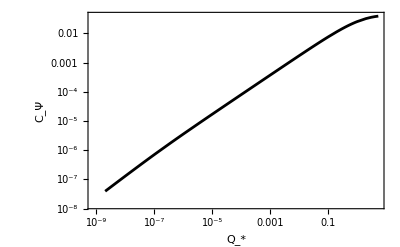

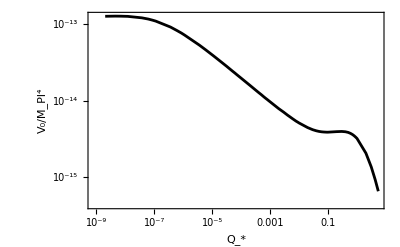

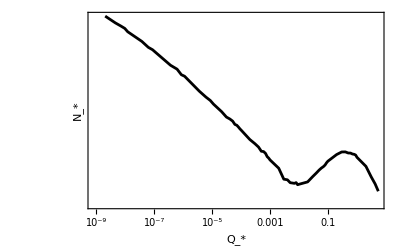

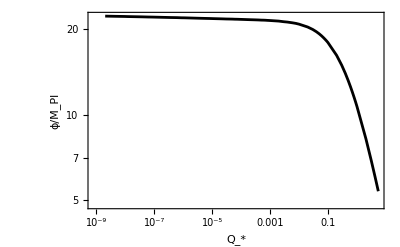

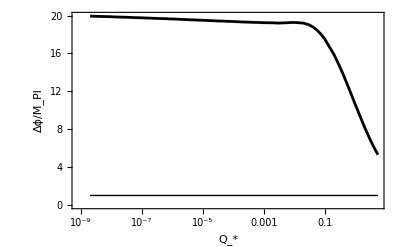

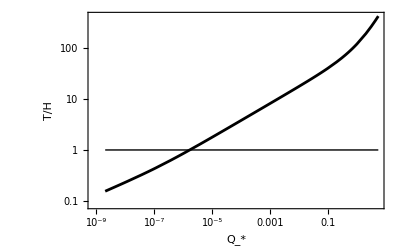

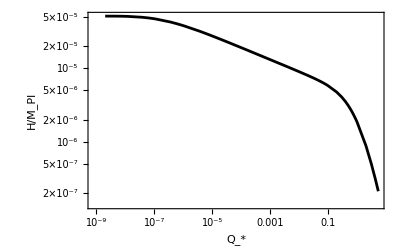

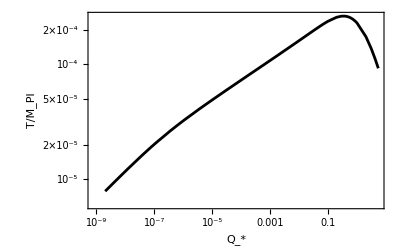

```mathematica
SetDirectory[NotebookDirectory[]]

(* data extracted from arXiv:2110.00483 
"BICEP/Keck XIII: Improved Constraints on Primordial Gravitational Waves using Planck, WMAP, and BICEP/Keck Observations through the 2018 Observing Season", Figure 5 *)

planck20181sigma=ReadList["planck2018_TT+TE+EE+lowE+lensing+BK18+BAO_68CL.dat",Number,RecordLists->True];
planck20182sigma=ReadList["planck2018_TT+TE+EE+lowE+lensing+BK18+BAO_95CL.dat",Number,RecordLists->True];
(*dataobs=Import[fileobs];*)
If[FileExistsQ[fileobs],dataobs=Import[fileobs],(*If file not found,prompt user to select it*)Print["Data file not found. Please select the input file."];
fileobs=SystemDialogInput["FileOpen",NotebookDirectory[]];
If[dataobs===$Canceled,Print["No file selected. Aborting."];
Abort[],dataobs=Import[fileobs]]];

CupsxQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[2]]},{k,Length[dataobs]}];
V0xQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[3]]},{k,Length[dataobs]}];
NstarxQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[4]]},{k,Length[dataobs]}];
phixQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[6]]},{k,Length[dataobs]}];
DeltaphixQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[7]]},{k,Length[dataobs]}];
THxQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[8]]},{k,Length[dataobs]}];
HxQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[9]]},{k,Length[dataobs]}];
TxQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[10]]},{k,Length[dataobs]}];
rxQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[11]]},{k,Length[dataobs]}];
nsxQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[12]]},{k,Length[dataobs]}];
dnsxQ=Table[{dataobs[[k]][[1]],dataobs[[k]][[13]]},{k,Length[dataobs]}];
nsxr=Table[{dataobs[[k]][[12]],dataobs[[k]][[11]]},{k,Length[dataobs]}];
tab1=Table[{dataobs[[k]][[1]],1},{k,Length[dataobs]}];
tab0p036=Table[{dataobs[[k]][[1]],0.036},{k,Length[dataobs]}];

ListLogLogPlot[CupsxQ,PlotStyle->{Black},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["C_Ψ",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All]

ListLogLogPlot[V0xQ,PlotStyle->{Black},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["V_0/M_Pl^4",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All]

ListLogLogPlot[{NstarxQ},PlotStyle->{Black},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["N_*",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All]

ListLogLogPlot[phixQ,PlotStyle->{Black},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["ϕ/M_Pl",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All]

ListLogLinearPlot[{DeltaphixQ,tab1},PlotStyle->{Black,{Black,Thin}},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["Δϕ/M_Pl",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All]

ListLogLogPlot[{THxQ,tab1},PlotStyle->{Black,{Black,Thin}},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["T/H",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All]

ListLogLogPlot[HxQ,PlotStyle->{Black},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["H/M_Pl",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All]

ListLogLogPlot[TxQ,PlotStyle->{Black},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["T/M_Pl",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All]

ListLogLogPlot[{rxQ,tab0p036},PlotStyle->{Black,{Red,Dashed}},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["r",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All,Filling->{2->{Top,LightGray}}]

rxQfunc=Interpolation[rxQ, Method->"Spline",InterpolationOrder->2];
Qrvalue=FindRoot[rxQfunc[x]==0.036,{x,dataobs[[1]][[1]],dataobs[[Length[dataobs]]][[1]]}][[1]][[2]];

ns1=ListLogLinearPlot[nsxQ,PlotStyle->{Black},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["n_s",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All];

pr=PlotRange/. AbsoluteOptions[ns1];

(*Convert the vertical line position to log scale (natural log)*)
logA=Log[Qrvalue];

ns1=ListLogLinearPlot[nsxQ,PlotStyle->{Black},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["n_s",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12],PlotRange->All,Prolog->{LightGray,Rectangle[{pr[[1,1]],pr[[2,1]]/2},(*x_min (log scale),y_min*){logA,pr[[2,2]]*2}          (*x=logA (log scale),y_max*)]}];

(*Draw the vertical line at x=logA (log scale)*)
verticalLine=Graphics[{Red,Dashed,Line[{{logA,pr[[2,1]]/2},{logA,pr[[2,2]]*2}}]}];

sigma1=LogLinearPlot[{0.9631058496475312,0.9699287452935624},{x,dataobs[[1]][[1]],dataobs[[Length[dataobs]]][[1]]},Filling->{1->{2}},FrameLabel->{StyleForm["Q_*", FontSize -> 14, Style -> {Italic}],StyleForm["n_s", FontSize -> 14, Style -> {Italic}]},LabelStyle->Directive[Black],
 FrameTicksStyle -> Directive[Black, 12],Frame->True,PlotStyle->None,FillingStyle->Directive[Opacity[0.4],Darker[Cyan]]];
sigma2=LogLinearPlot[{0.9585382838793183,0.9740831124164718},{x,dataobs[[1]][[1]],dataobs[[Length[dataobs]]][[1]]},Filling->{1->{2}},FrameLabel->{StyleForm["Q_*", FontSize -> 14, Style -> {Italic}],StyleForm["n_s", FontSize -> 14, Style -> {Italic}]},LabelStyle->Directive[Black],
 FrameTicksStyle -> Directive[Black, 12],Frame->True,PlotStyle->None,FillingStyle->Directive[Opacity[0.4],Darker[Cyan]]];

(*Combine all components*)
Show[ns1,sigma1,sigma2,(*filledRegion,*)verticalLine,PlotRange->pr]

p1=ListLogPlot[{planck20181sigma,planck20182sigma},PlotRange->{{0.95,1},{dataobs[[Length[dataobs]]][[11]],1}},Joined->True,Filling->Axis,FillingStyle->Directive[Opacity[0.1],Cyan],
 FrameTicksStyle -> Directive[Black, 12],
 Frame -> True,FrameLabel->{StyleForm["n_s", FontSize -> 14, Style -> {Italic},FontColor->Black],StyleForm["r", FontSize -> 14, Style -> {Italic},FontColor->Black]}];
p2=ListLogPlot[nsxr,PlotStyle->{Black},PlotRange->{{0.95,1},{dataobs[[Length[dataobs]]][[11]],1}},Joined->True,
 FrameTicksStyle -> Directive[Black, 12],
 Frame -> True,FrameLabel->{StyleForm["n_s", FontSize -> 14, Style -> {Italic},FontColor->Black],StyleForm["r", FontSize -> 14, Style -> {Italic},FontColor->Black]}];
Show[{p1,p2}]

ListLogLinearPlot[dnsxQ,PlotStyle->{Black},Frame-> True,Joined->True,FrameLabel->{Style["Q_*",  14, Italic,Black],Style["α_s",Italic,14,Black]},
 FrameTicksStyle -> Directive[Black, 12](*,PlotRange->All*)]
```

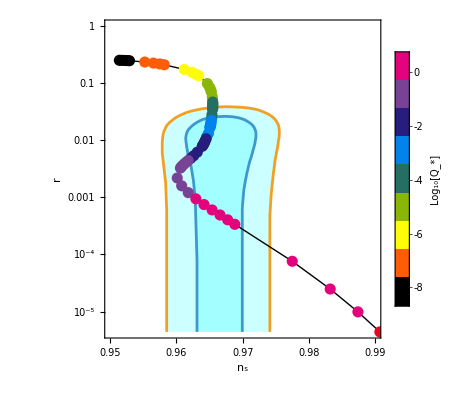

```mathematica
p1t=ListLogPlot[{planck20181sigma,planck20182sigma},PlotRange->{{0.95,0.99},{dataobs[[Length[dataobs]]][[11]],1}},Joined->True,PlotStyle->Automatic,Filling->Axis,FillingStyle->Directive[(*Opacity[0.4],(*Orange*)#aa0000*)Opacity[0.2],Cyan],
 FrameTicksStyle -> Directive[Black, 12],
 Frame -> True,FrameLabel->{StyleForm["n_s", FontSize -> 14, Style -> {Italic},FontColor->Black],StyleForm["r", FontSize -> 14, Style -> {Italic},FontColor->Black]},AspectRatio->1];

(*Create associations to map t->x and t->y*)(*Round t values to 6 decimal places*)
dataXT=rxQ;
dataYT=nsxQ;

(*Create associations with rounded t-values to avoid precision mismatches*)
xtAssoc=Association[Thread[Round[dataXT[[All,1]],10^-9]->dataXT[[All,2]]]];(*Fixed:Added] after dataXT[[All,2]]*)ytAssoc=Association[Thread[Round[dataYT[[All,1]],10^-9]->dataYT[[All,2]]]];(*Fixed:Added] after dataYT[[All,2]]*)(*Find common t values*)commonTs=Intersection[Keys[xtAssoc],Keys[ytAssoc]];
(*Check if commonTs is populated*)If[Length[commonTs]==0,Print["ERROR: No common t values found. Check data alignment."],(*Proceed if commonTs is non-empty*)combinedData={xtAssoc[#],ytAssoc[#],#}&/@commonTs;
minT=Min[combinedData[[All,3]]];
maxT=Max[combinedData[[All,3]]];
(*maxT=40;*)
minLogT=Log10[minT];  (*Minimum log10(t)*)maxLogT=Log10[maxT];  (*Maximum log10(t)*)

(*Generate log-scaled ticks for the bar legend*)linearTicks=FindDivisions[{minT,maxT},5];  (*Find 5 nice linear divisions*)logTicks=Transpose[{Log10[linearTicks],(*Positions in log scale*)linearTicks          (*Labels as original t values*)}];

(*Style points:color scaled to log10(t)*)

numColors=10;styledData=Style[{#[[2]],#[[1]]},(*Plot {y,x}*)PointSize[0.02],(*Adjust point size*)ColorData[3][Floor[Rescale[Log10[#[[3]]],{minLogT,maxLogT},{1,numColors}]]](*Log color scaling*)]&/@combinedData;

(*Create plot with log-scaled bar legend*)plot=Legended[ListPlot[styledData,ScalingFunctions->"Log",
 FrameTicksStyle -> Directive[Black, 12],
 Frame -> True,Joined-> True,PlotStyle-> {Black,Thin},FrameLabel->{StyleForm["n_s", FontSize -> 14,FontColor->Black, Style -> {Italic}],StyleForm["r", FontSize -> 14, Style -> {Italic},FontColor->Black]},PlotStyle->PointSize[0.02]],BarLegend[{3,{minLogT,maxLogT}},LegendLabel->"Log_10[Q_*]"]];
]

Show[{p1t,plot}]

Show[{p1t,plot}]//Export["rXns.pdf",#,ImageSize->300]&;
```